# Euler-type quadrature formulas - Gregory’s formula

## Trapezium formula

```mathematica
Clear[trapezoidalFormula]
trapezoidalFormula[f_,{a_Real,b_Real},n_Integer]:=Module[
{
h=(b-a)/n,
xk
},
xk=Table[a+h i,{i,0,n}];
N[h/2((f/.x->xk⟦1⟧)+2Sum[(f/.x->xk⟦i⟧),{i,2,n}]+(f/.x->xk⟦n+1⟧))]]
```

## Finite Difference Calculation

```mathematica
Clear[finiteDifferences]
finiteDifferences[y_List]:=Module[
{
n=Length[y],
coef
},
coef=ConstantArray[0,{n,6}];
coef⟦All,1⟧=y;
Do[
coef⟦i,j⟧=coef⟦i+1,j-1⟧-coef⟦i,j-1⟧,
{j,2,6},{i,n-j+1}];
coef
]
```

## Formula Gregory

```mathematica
Clear[gregory]
gregory[f_,{a_Real,b_Real},n_Integer]:=Module[
{
h=(b-a)/n,
xk,
y,
coefs
},
xk=Table[a+h i,{i,0,n}];
y=Composition[N,f/.x->#&][Range[n]];
coefs=finiteDifferences[y];
trapezoidalFormula[f,{a,b},n]-h/12(coefs⟦n-1,1⟧-coefs⟦1,1⟧)-h/24(coefs⟦n-2,2⟧-coefs⟦1,2⟧)-(19h)/720(coefs⟦n-3,3⟧-coefs⟦1,3⟧)-(3h)/160(coefs⟦n-4,4⟧-coefs⟦1,4⟧)-(863h)/60480(coefs⟦n-6,6⟧-coefs⟦1,6⟧)
]
```

## Example №1

```mathematica
f1=Sin[x^2]+1;
```

```mathematica
NIntegrate[f1,{x,1,10}]
```

9.2734

```mathematica
gregory[f1,{1.,10.},150000]
```

gregory[1+Sin[x^2],{1.,10.},150000]

```mathematica
res1=ConstantArray[NIntegrate[f1,{x,1,10}],500-6];
```

```mathematica
test1=Table[gregory[f1,{1.,10.},i],{i,7,500}];
```

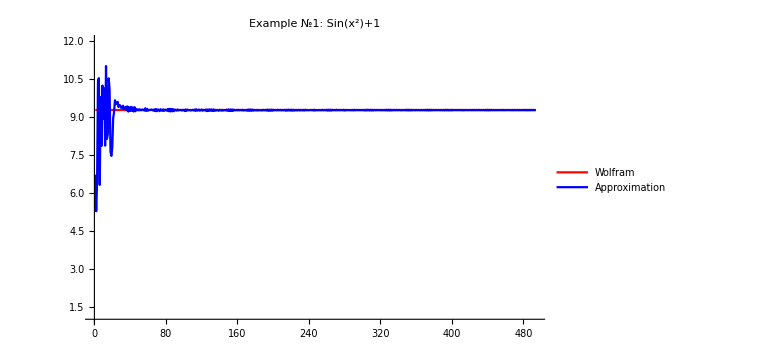

```mathematica
ListLinePlot[{res1,test1},
PlotRange->{1,12},
PlotLegends->{"Wolfram","Approximation"},
PlotLabel->Style[Framed["Example №1: Sin(x^2)+1"],16,Bold,Black],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```

## Example №2

```mathematica
f2=x/(1+x);
```

```mathematica
NIntegrate[f2,{x,1,5}]
```

2.90139

```mathematica
gregory[f2,{1.,5.},100000]
```

2.90139

```mathematica
res2=ConstantArray[NIntegrate[f2,{x,1,5}],500-7];
```

```mathematica
test2=Table[gregory[f2,{1.,5.},i],{i,7,500}];
```

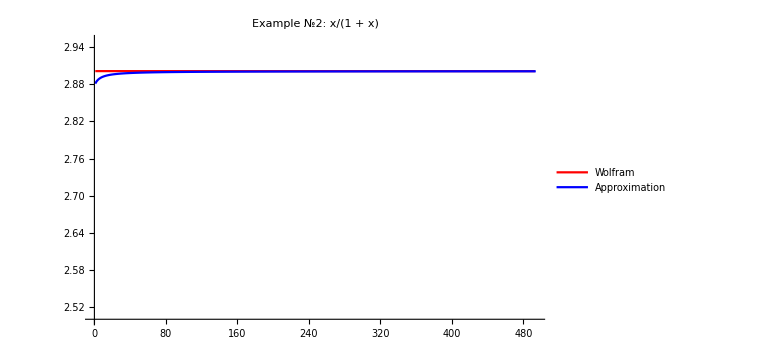

```mathematica
ListLinePlot[{res2,test2},
PlotRange->{{2.5,2.95}},
PlotLegends->{"Wolfram","Approximation"},
PlotLabel->Style[Framed["Example №2: x/(1 + x)"],16,Bold,Black],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```

## Example №3

```mathematica
f3=√(1+1/x);
```

```mathematica
NIntegrate[f3,{x,1,4}]
```

3.62018

```mathematica
gregory[f3,{1.,4.},120000]
```

3.62018

```mathematica
res3=ConstantArray[NIntegrate[f3,{x,1,4}],500-7];
```

```mathematica
test3=Table[gregory[f3,{1.,4.},i],{i,7,500}];
```

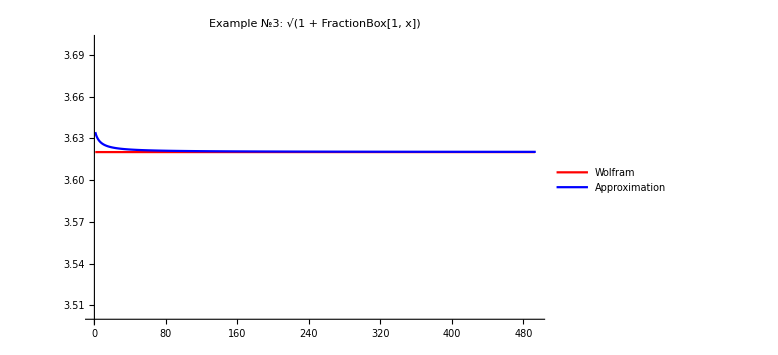

```mathematica
ListLinePlot[{res3,test3},
PlotRange->{3.5,3.7},
PlotLegends->{"Wolfram","Approximation"},
PlotLabel->Style[Framed["Example №3: √(1 + FractionBox[1, x])"],16,Bold,Black],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```

## Example №4

```mathematica
f4=Sin[Sin[x]];
```

```mathematica
NIntegrate[f4,{x,0,4}]
```

1.45747

```mathematica
gregory[f4,{0.,4.},10000]
```

1.45747

```mathematica
res4=ConstantArray[NIntegrate[f4,{x,0,4}],1000-7];
```

```mathematica
test4=Table[gregory[f4,{0.,4.},i],{i,7,1000}];
```

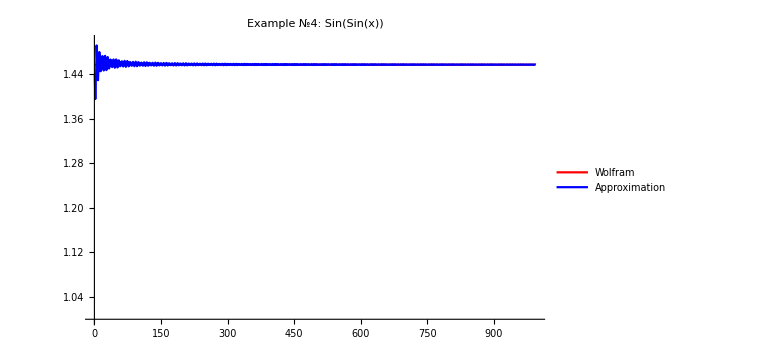

```mathematica
ListLinePlot[{res4,test4},
PlotRange->{1,1.5},
PlotLegends->{"Wolfram","Approximation"},
PlotLabel->Style[Framed["Example №4: Sin(Sin(x))"],16,Bold,Black],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```